```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY201/sec_int_data/500nm.dat"]
```

{{1.59376,0.221943},{1.5163,0.24373},{1.45822,0.247953},{1.41492,0.228807},{1.36475,0.238387},{1.33366,0.264055},{1.2821,0.272086},{1.25075,0.26651},{1.2275,0.26221},{1.20277,0.268576},{1.18632,0.273989},{1.16701,0.264439},{1.14926,0.257584},{1.12973,0.224263},{1.10588,-0.992497},{1.11907,0.224103},{1.13878,0.30697},{1.30525,0.227773},{1.35407,0.175549}}

-0.470839+0.511207 x

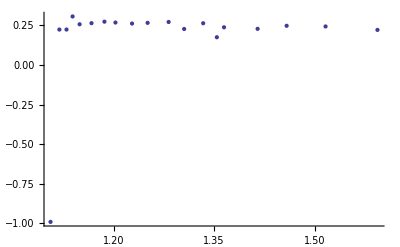

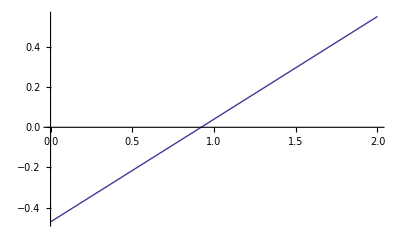

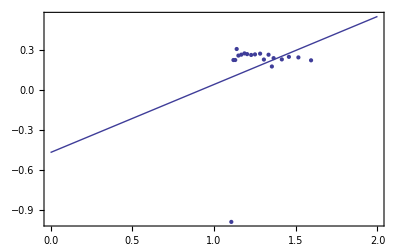

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```